```mathematica
mydata=Import[StringJoin[NotebookDirectory[],"data/exampleFreezeOut.mx"]]
```

<|BackgroundFields→{{0.0301913,0.14,-0.000263747,0.000523539,-0.000383441},{0.0502814,0.14,-0.000264206,0.000517444,-0.000383448},{0.0703157,0.14,-0.000264878,0.000508303,-0.000383461},{0.0902726,0.14,-0.00026574,0.000496113,-0.000383484},{0.110131,0.14,-0.000266767,0.00048087,-0.00038352},{0.129872,0.14,-0.000267927,0.000462562,-0.000383573},{0.149474,0.14,-0.000269178,0.000441166,-0.00038365},{0.168921,0.14,-0.000270474,0.000416666,-0.00038375},{0.188195,0.14,-0.000271748,0.000389041,-0.000383876},{0.207277,0.14,-0.000272915,0.00035828,-0.000384029},{0.226153,0.14,-0.000273858,0.000324375,-0.000384214},{0.244806,0.14,-0.000274432,0.000287349,-0.000384434},{0.26322,0.14,-0.000274456,0.000247245,-0.000384695},{0.281383,0.14,-0.000273715,0.00020413,-0.000385003},{0.299279,0.14,-0.000271961,0.000158094,-0.000385372},{0.316898,0.14,-0.000268913,0.00010924,-0.000385815},{0.334228,0.14,-0.000264247,0.0000576671,-0.000386359},{0.351261,0.14,-0.000257662,3.58368×10^-6,-0.000386997},{0.367989,0.14,-0.000248754,-0.0000529206,-0.000387774},{0.369078,0.14,-0.000248,-0.0000567812,-0.000387837},{0.384407,0.14,-0.000237122,-0.000111688,-0.000388714},{0.387938,0.14,-0.000233943,-0.00012492,-0.000388964},{0.400511,0.14,-0.000222339,-0.000172559,-0.000389847},{0.4163,0.14,-0.000203941,-0.000235413,-0.000391213},{0.431777,0.14,-0.000181504,-0.000300082,-0.000392839},{0.439933,0.14,-0.000167225,-0.000335537,-0.00039387},{0.446949,0.14,-0.000154561,-0.000366491,-0.000394766},{0.448372,0.14,-0.000151583,-0.000372927,-0.000394984},{0.454759,0.14,-0.000138008,-0.000402031,-0.000395965},{0.461822,0.14,-0.000122583,-0.000434659,-0.000397057},{0.476409,0.14,-0.0000850617,-0.000504617,-0.00039976},{0.482249,0.14,-0.0000676587,-0.000533577,-0.000401032},{0.490729,0.14,-0.0000415269,-0.000576401,-0.000402913},{0.493335,0.14,-0.0000324758,-0.00058988,-0.000403586},{0.497334,0.14,-0.0000183745,-0.000610736,-0.000404627},{0.504798,0.14,8.70081×10^-6,-0.000650299,-0.000406604},{0.515718,0.14,0.0000536964,-0.00071015,-0.000409958},{0.518644,0.14,0.0000661801,-0.000726523,-0.000410877},{0.519898,0.14,0.0000720122,-0.000733644,-0.000411323},{0.52331,0.14,0.0000880708,-0.000753162,-0.000412546},{0.526896,0.14,0.000105258,-0.000773908,-0.000413847},{0.532294,0.14,0.000131769,-0.000805626,-0.000415842},{0.539791,0.14,0.000172488,-0.000850968,-0.000418984},{0.545784,0.14,0.000206279,-0.000888127,-0.000421567},{0.547032,0.14,0.000213916,-0.000896041,-0.00042217},{0.549116,0.14,0.000226787,-0.00090934,-0.000423183},{0.55145,0.14,0.000241384,-0.000924361,-0.000424327},{0.559151,0.14,0.00029099,-0.000974959,-0.000428193},{0.561539,0.14,0.000307715,-0.000991094,-0.000429528},{0.564104,0.14,0.00032598,-0.00100864,-0.000430984},{0.566459,0.14,0.000343,-0.00102492,-0.000432336},{0.569305,0.14,0.000363905,-0.00104483,-0.000433992},{0.572444,0.14,0.000387405,-0.00106709,-0.000435847},{0.580103,0.14,0.000449904,-0.00112337,-0.000440899},{0.585714,0.14,0.000497753,-0.00116596,-0.000444737},{0.588736,0.14,0.000525591,-0.00118967,-0.000447025},{0.590228,0.14,0.000539563,-0.00120153,-0.00044817},{0.592149,0.14,0.000557756,-0.00121692,-0.00044966},{0.593986,0.14,0.000575394,-0.0012318,-0.0004511},{0.59903,0.14,0.000625062,-0.00127344,-0.000455144},{0.599381,0.14,0.000628728,-0.00127641,-0.000455448},{0.603654,0.14,0.000674374,-0.0013132,-0.000459248},{0.605449,0.14,0.000693988,-0.00132892,-0.000460876},{0.607153,0.14,0.00071287,-0.00134402,-0.000462441},{0.60874,0.14,0.000730666,-0.00135822,-0.000463914},{0.612482,0.14,0.000773578,-0.0013923,-0.000467459},{0.616307,0.14,0.000820638,-0.0014285,-0.000471428},{0.617729,0.14,0.000838528,-0.00144221,-0.000472934},{0.619444,0.14,0.000860375,-0.00145891,-0.000474772},{0.620704,0.14,0.00087665,-0.00147132,-0.000476139},{0.622214,0.14,0.000896361,-0.00148632,-0.000477792},{0.626193,0.14,0.000949575,-0.00152666,-0.000482246},{0.627106,0.14,0.000962529,-0.00153624,-0.000483353},{0.629409,0.14,0.000995712,-0.00156073,-0.000486188},{0.630786,0.14,0.00101589,-0.00157558,-0.000487908},{0.632121,0.14,0.0010357,-0.00159014,-0.000489597},{0.633447,0.14,0.00105561,-0.00160474,-0.000491291},{0.636916,0.14,0.00110892,-0.00164369,-0.000495819},{0.638604,0.14,0.00113549,-0.00166305,-0.000498071},{0.640343,0.14,0.00116334,-0.00168328,-0.000500429},{0.641149,0.14,0.00117689,-0.00169295,-0.000501599},{0.642359,0.14,0.00119744,-0.0017076,-0.000503375},{0.645604,0.14,0.00125385,-0.00174769,-0.00050824},{0.647296,0.14,0.00128401,-0.00176906,-0.000510837},{0.648426,0.14,0.00130448,-0.00178354,-0.000512598},{0.649495,0.14,0.00132405,-0.00179736,-0.00051428},{0.650556,0.14,0.00134371,-0.00181123,-0.000515968},{0.655223,0.14,0.00143288,-0.00187395,-0.000523612},{0.655787,0.14,0.00144436,-0.00188191,-0.000524614},{0.657,0.14,0.00146931,-0.00189921,-0.000526792},{0.65783,0.14,0.00148657,-0.00191116,-0.000528297},{0.65879,0.14,0.00150676,-0.00192514,-0.000530057},{0.661163,0.14,0.00155764,-0.0019603,-0.000534489},{0.663523,0.14,0.00160972,-0.00199624,-0.00053902},{0.664501,0.14,0.00163174,-0.00201142,-0.000540933},{0.665526,0.14,0.0016551,-0.00202751,-0.000542962},{0.666488,0.14,0.0016773,-0.00204279,-0.00054489},{0.667443,0.14,0.00169962,-0.00205815,-0.000546826},{0.671387,0.14,0.00179472,-0.00212351,-0.000555067},{0.672354,0.14,0.00181955,-0.00214047,-0.000557254},{0.673531,0.14,0.00185024,-0.00216142,-0.000559956},{0.674267,0.14,0.00186969,-0.0021747,-0.000561668},{0.675133,0.14,0.00189282,-0.00219049,-0.000563703},{0.67727,0.14,0.00195114,-0.00223031,-0.00056883},{0.678696,0.14,0.00199107,-0.00225757,-0.000572338},{0.67972,0.14,0.00202028,-0.00227752,-0.000574902},{0.680354,0.14,0.00203857,-0.00229001,-0.000576507},{0.681079,0.14,0.00205973,-0.00230447,-0.000578364},{0.6818,0.14,0.00208099,-0.002319,-0.000580228},{0.684636,0.14,0.00216694,-0.00237777,-0.00058776},{0.685285,0.14,0.00218718,-0.00239162,-0.000589532},{0.686103,0.14,0.00221297,-0.00240927,-0.00059179},{0.686727,0.14,0.00223287,-0.0024229,-0.000593531},{0.687478,0.14,0.00225709,-0.0024395,-0.00059565},{0.69024,0.14,0.00234899,-0.00250254,-0.000603684},{0.692162,0.14,0.00241726,-0.00254943,-0.00060973},{0.692919,0.14,0.00244486,-0.00256841,-0.000612174},{0.693763,0.14,0.00247609,-0.00258992,-0.000614939},{0.694334,0.14,0.00249751,-0.00260469,-0.000616835},{0.695007,0.14,0.00252303,-0.0026223,-0.000619094},{0.696665,0.14,0.00258738,-0.00266679,-0.000624788},{0.698113,0.14,0.00264533,-0.00270697,-0.000629914},{0.69926,0.14,0.00269246,-0.00273971,-0.000634081},{0.699786,0.14,0.00271442,-0.002755,-0.000636023},{0.700402,0.14,0.00274049,-0.00277317,-0.000638327},{0.701921,0.14,0.00280622,-0.00281909,-0.000644137},{0.703402,0.14,0.00287247,-0.00286554,-0.000649991},{0.704184,0.14,0.00290836,-0.00289078,-0.000653162},{0.704801,0.14,0.00293715,-0.00291106,-0.000655705},{0.705407,0.14,0.00296585,-0.00293132,-0.000658241},{0.706997,0.14,0.00304309,-0.00298602,-0.000665063},{0.708179,0.14,0.0031025,-0.00302828,-0.000670311},{0.708625,0.14,0.0031254,-0.00304461,-0.000672333},{0.709114,0.14,0.00315082,-0.00306278,-0.000674579},{0.710319,0.14,0.00321487,-0.00310868,-0.000680235},{0.711525,0.14,0.00328113,-0.0031564,-0.000686087},{0.712043,0.14,0.00331029,-0.00317747,-0.000688662},{0.712579,0.14,0.00334091,-0.00319964,-0.000691366},{0.713066,0.14,0.00336917,-0.00322015,-0.000693862},{0.713548,0.14,0.00339757,-0.0032408,-0.000696369},{0.715429,0.14,0.00351247,-0.00332483,-0.000706516},{0.71609,0.14,0.00355453,-0.00335578,-0.000710231},{0.716739,0.14,0.00359673,-0.00338693,-0.000713958},{0.71712,0.14,0.00362202,-0.00340565,-0.000716192},{0.717561,0.14,0.00365161,-0.0034276,-0.000718805},{0.71864,0.14,0.00372616,-0.00348314,-0.00072539},{0.719783,0.14,0.00380859,-0.00354494,-0.000732673},{0.72038,0.14,0.00385315,-0.00357851,-0.00073661},{0.720807,0.14,0.00388566,-0.00360309,-0.000739483},{0.721199,0.14,0.00391613,-0.00362618,-0.000742175},{0.721587,0.14,0.00394674,-0.00364944,-0.00074488},{0.72309,0.14,0.00407058,-0.00374415,-0.000755829},{0.724038,0.14,0.00415348,-0.00380809,-0.000763161},{0.724484,0.14,0.0041939,-0.00383943,-0.000766737},{0.724854,0.14,0.0042282,-0.00386611,-0.000769772},{0.725139,0.14,0.00425512,-0.0038871,-0.000772154},{0.72542,0.14,0.00428214,-0.00390822,-0.000774546},{0.726512,0.14,0.00439126,-0.003994,-0.000784209},{0.726817,0.14,0.00442314,-0.00401922,-0.000787034},{0.72712,0.14,0.00445546,-0.00404485,-0.000789899},{0.727421,0.14,0.00448823,-0.00407091,-0.000792803},{0.728135,0.14,0.00456875,-0.00413525,-0.000799944},{0.72882,0.14,0.00465017,-0.00420077,-0.00080717},{0.729142,0.14,0.00469003,-0.00423301,-0.000810709},{0.729404,0.14,0.00472334,-0.00426005,-0.000813668},{0.729662,0.14,0.0047568,-0.00428728,-0.000816641},{0.730644,0.14,0.00489214,-0.00439824,-0.000828676},{0.730977,0.14,0.00494126,-0.00443883,-0.000833048},{0.731312,0.14,0.00499241,-0.00448128,-0.000837603},{0.731502,0.14,0.00502244,-0.0045063,-0.000840278},{0.73171,0.14,0.00505607,-0.00453439,-0.000843275},{0.732211,0.14,0.00514078,-0.00460551,-0.000850829},{0.732701,0.14,0.00522982,-0.00468083,-0.000858775},{0.732916,0.14,0.00527122,-0.00471605,-0.000862472},{0.733132,0.14,0.00531419,-0.00475275,-0.000866311},{0.733304,0.14,0.00534966,-0.00478313,-0.00086948},{0.733472,0.14,0.00538527,-0.00481374,-0.000872664},{0.734094,0.14,0.00552928,-0.00493844,-0.000885547},{0.734388,0.14,0.00560537,-0.00500495,-0.000892358},{0.73462,0.14,0.00567019,-0.00506194,-0.000898163},{0.734728,0.14,0.00570174,-0.00508979,-0.000900989},{0.734847,0.14,0.00573838,-0.00512223,-0.000904271},{0.735127,0.14,0.00583068,-0.00520438,-0.000912541},{0.73541,0.14,0.00593713,-0.00529989,-0.000922079},{0.735561,0.14,0.00600128,-0.00535784,-0.000927825},{0.735651,0.14,0.00604306,-0.00539575,-0.000931568},{0.735728,0.14,0.00608083,-0.00543011,-0.00093495},{0.7358,0.14,0.00611875,-0.00546472,-0.000938345},{0.736043,0.14,0.00627207,-0.00560568,-0.000952059},{0.736135,0.14,0.00634836,-0.00567644,-0.000958873},{0.736202,0.14,0.00641633,-0.00573981,-0.000964937},{0.736231,0.14,0.00645051,-0.00577179,-0.000967983},{0.736258,0.14,0.00648932,-0.00580821,-0.00097144},{0.736309,0.14,0.00658709,-0.00590038,-0.000980132},{0.736332,0.14,0.00668841,-0.00599655,-0.000989115},{0.736332,0.14,0.00673329,-0.00603935,-0.000993084},{0.736327,0.14,0.00678414,-0.00608801,-0.000997575},{0.736317,0.14,0.00682422,-0.00612646,-0.00100111},{0.736303,0.14,0.00686447,-0.00616517,-0.00100465},{0.736106,0.14,0.00702585,-0.00632382,-0.00101955},{0.73594,0.14,0.00711582,-0.00641371,-0.00102804},{0.735808,0.14,0.00717972,-0.00647796,-0.00103408},{0.735725,0.14,0.00721706,-0.00651565,-0.00103761},{0.73563,0.14,0.00725772,-0.00655683,-0.00104146},{0.73553,0.14,0.00729853,-0.00659829,-0.00104532},{0.735206,0.14,0.00741976,-0.00672225,-0.00105681},{0.734973,0.14,0.00749848,-0.00680337,-0.00106427},{0.734807,0.14,0.00755146,-0.00685825,-0.00106929},{0.734557,0.14,0.0076271,-0.00693698,-0.00107646},{0.734208,0.14,0.00772586,-0.00704046,-0.0010858},{0.733895,0.14,0.00780876,-0.0071279,-0.00109364},{0.733746,0.14,0.00784655,-0.00716793,-0.00109721},{0.733575,0.14,0.00788897,-0.007213,-0.00110121},{0.733124,0.14,0.00799572,-0.00732703,-0.00111126},{0.7326,0.14,0.00811208,-0.00745226,-0.00112217},{0.732314,0.14,0.00817276,-0.00751794,-0.00112784},{0.732068,0.14,0.00822359,-0.00757316,-0.00113257},{0.731851,0.14,0.00826719,-0.00762068,-0.00113662},{0.731331,0.14,0.00836837,-0.00773141,-0.00114599},{0.730376,0.14,0.00854361,-0.00792468,-0.00116204},{0.729666,0.14,0.00866619,-0.0080609,-0.00117314},{0.729211,0.14,0.00873337,-0.0081379,-0.00117979},{0.728824,0.14,0.00878492,-0.00819838,-0.00118523},{0.728492,0.14,0.00882845,-0.0082497,-0.00118983},{0.728153,0.14,0.00887211,-0.00830139,-0.00119444},{0.72673,0.14,0.009048,-0.00851184,-0.00121305},{0.725589,0.14,0.00918163,-0.0086741,-0.00122717},{0.724789,0.14,0.00927186,-0.00878484,-0.0012367},{0.724305,0.14,0.00932507,-0.00885056,-0.0012423},{0.723734,0.14,0.00938682,-0.00892725,-0.0012488},{0.722751,0.14,0.00949027,-0.00905666,-0.00125964},{0.721714,0.14,0.00959603,-0.00919016,-0.00127067},{0.721089,0.14,0.00965818,-0.00926917,-0.00127712},{0.720565,0.14,0.00970945,-0.00933465,-0.00128242},{0.719553,0.14,0.00980626,-0.00945903,-0.00129237},{0.718949,0.14,0.0098628,-0.00953209,-0.00129814},{0.71818,0.14,0.00993362,-0.00962405,-0.00130533},{0.716964,0.14,0.0100428,-0.00976666,-0.00131629},{0.715255,0.14,0.010191,-0.00996207,-0.00133095},{0.713822,0.14,0.0103111,-0.0101217,-0.0013426},{0.71325,0.14,0.010358,-0.0101843,-0.00134708},{0.712636,0.14,0.0104058,-0.0102497,-0.001352},{0.71096,0.14,0.0105192,-0.0104163,-0.0013664},{0.709218,0.14,0.0106329,-0.0105861,-0.00138086},{0.708501,0.14,0.0106785,-0.0106549,-0.00138665},{0.707648,0.14,0.010732,-0.0107362,-0.00139345},{0.706652,0.14,0.0107934,-0.0108302,-0.00140123},{0.704235,0.14,0.0109374,-0.0110541,-0.00141944},{0.701381,0.14,0.0110997,-0.0113115,-0.0014398},{0.700402,0.14,0.0111536,-0.0113981,-0.0014465},{0.699384,0.14,0.0112086,-0.0114873,-0.00145332},{0.696577,0.14,0.0113556,-0.0117287,-0.00147135},{0.695448,0.14,0.0114129,-0.011824,-0.0014783},{0.694224,0.14,0.0114739,-0.0119262,-0.00148563},{0.692127,0.14,0.0115756,-0.0120986,-0.00149771},{0.688622,0.14,0.0117387,-0.0123796,-0.00151664},{0.687267,0.14,0.0117995,-0.0124859,-0.00152354},{0.685664,0.14,0.0118698,-0.0126099,-0.0015314},{0.684047,0.14,0.0119392,-0.0127334,-0.00153903},{0.681676,0.14,0.0120379,-0.0129113,-0.00154966},{0.679281,0.14,0.0121261,-0.0130859,-0.00156247},{0.677464,0.14,0.0121873,-0.0132158,-0.00157305},{0.674939,0.14,0.0122698,-0.0133938,-0.00158731},{0.672731,0.14,0.0123393,-0.0135471,-0.00159936},{0.670869,0.14,0.0123963,-0.0136746,-0.00160921},{0.667284,0.14,0.0125017,-0.013916,-0.00162743},{0.662978,0.14,0.0126213,-0.0141986,-0.00164801},{0.6612,0.14,0.0126686,-0.0143131,-0.0016561},{0.659277,0.14,0.0127184,-0.0144355,-0.0016646},{0.653945,0.14,0.0128497,-0.0147669,-0.00168676},{0.649914,0.14,0.0129426,-0.0150102,-0.00170222},{0.647364,0.14,0.0129987,-0.0151609,-0.00171144},{0.645037,0.14,0.0130482,-0.0152964,-0.0017195},{0.641556,0.14,0.0131192,-0.0154956,-0.00173093},{0.637955,0.14,0.0131891,-0.0156972,-0.00174199},{0.631507,0.14,0.0133055,-0.0160474,-0.00175999},{0.623858,0.14,0.0134301,-0.0164464,-0.00177852},{0.621546,0.14,0.0134651,-0.0165636,-0.00178357},{0.619471,0.14,0.0134954,-0.0166675,-0.00178789},{0.616766,0.14,0.0135335,-0.0168011,-0.00179323},{0.614,0.14,0.0135709,-0.0169358,-0.00179837},{0.60673,0.14,0.0136571,-0.0172818,-0.00181455},{0.598357,0.14,0.013736,-0.0176661,-0.00183934},{0.58945,0.14,0.013809,-0.0180545,-0.00186297},{0.58612,0.14,0.0138336,-0.0181945,-0.00187113},{0.583343,0.14,0.0138531,-0.0183092,-0.00187768},{0.580702,0.14,0.0138708,-0.0184164,-0.00188369},{0.577238,0.14,0.0138928,-0.0185546,-0.00189127},{0.573695,0.14,0.0139139,-0.0186929,-0.00189869},{0.563937,0.14,0.0139655,-0.0190588,-0.00191749},{0.552365,0.14,0.0140152,-0.0194655,-0.00193705},{0.548617,0.14,0.0140288,-0.0195911,-0.00194284},{0.544649,0.14,0.0140421,-0.019721,-0.0019487},{0.540665,0.14,0.0140542,-0.0198482,-0.00195435},{0.536595,0.14,0.0140653,-0.0199749,-0.00195987},{0.526033,0.14,0.0140889,-0.0202889,-0.00197325},{0.514639,0.14,0.0141064,-0.0206046,-0.00198643},{0.502613,0.14,0.0141168,-0.0209132,-0.00199936},{0.497313,0.14,0.0141189,-0.0210413,-0.00200486},{0.492805,0.14,0.0141196,-0.0211468,-0.00200948},{0.486474,0.14,0.0141188,-0.0212893,-0.00201591},{0.479084,0.14,0.0141156,-0.0214476,-0.00202342},{0.458329,0.14,0.0140934,-0.0218477,-0.00204516},{0.445087,0.14,0.0140698,-0.02207,-0.00206014},{0.431281,0.14,0.0140375,-0.0222754,-0.00207718},{0.425173,0.14,0.0140208,-0.0223578,-0.00208529},{0.419891,0.14,0.0140051,-0.0224251,-0.00209262},{0.412802,0.14,0.0139822,-0.0225093,-0.00210297},{0.404704,0.14,0.0139534,-0.0225973,-0.00211556},{0.382362,0.14,0.0138594,-0.0227946,-0.00215504},{0.359018,0.14,0.013736,-0.0229292,-0.0022049},{0.344742,0.14,0.0136463,-0.0229746,-0.00224028},{0.330197,0.14,0.0135426,-0.0229909,-0.00228048},{0.321876,0.14,0.0134772,-0.0229861,-0.00230546},{0.315217,0.14,0.0134214,-0.0229745,-0.00232653},{0.307597,0.14,0.0133535,-0.0229526,-0.00235182},{0.299471,0.14,0.0132762,-0.0229186,-0.00238022},{0.277622,0.14,0.01304,-0.022769,-0.00246394},{0.259233,0.14,0.0128047,-0.0225699,-0.00254255},{0.244425,0.14,0.0125869,-0.0223541,-0.00261081},{0.2332,0.14,0.0124028,-0.0221533,-0.00266504},{0.225559,0.14,0.012267,-0.0219965,-0.0027029},{0.217821,0.14,0.0121203,-0.0218197,-0.00274179},{0.20999,0.14,0.0119616,-0.021621,-0.0027814},{0.198359,0.14,0.0117056,-0.0212859,-0.00283992},{0.182978,0.14,0.0113256,-0.020761,-0.00291426},{0.167685,0.14,0.0108952,-0.0201335,-0.00298022},{0.161596,0.14,0.0107076,-0.0198508,-0.00300285},{0.155519,0.14,0.0105105,-0.0195484,-0.00302265},{0.148139,0.14,0.0102572,-0.0191523,-0.00304212},{0.133721,0.14,0.00971377,-0.0182767,-0.00306119},{0.132146,0.14,0.00964869,-0.0181731,-0.00306741},{0.120419,0.14,0.00912853,-0.0173218,-0.00310148},{0.107291,0.14,0.008487,-0.0162334,-0.00311014},{0.0920309,0.14,0.00765499,-0.0147694,-0.00306426},{0.0858833,0.14,0.00729145,-0.0141143,-0.00302359},{0.075943,0.14,0.00666663,-0.0129699,-0.00292444},{0.0672738,0.14,0.00608226,-0.0118817,-0.00279874},{0.0565046,0.14,0.00530176,-0.010406,-0.00258295},{0.042793,0.14,0.00421373,-0.00831537,-0.00219686},{0.0343502,0.14,0.00348698,-0.00690206,-0.00188895},{0.0272833,0.14,0.00284265,-0.00564004,-0.00158627},{0.0205962,0.14,0.00220056,-0.00437532,-0.00126003},{0.0123098,0.14,0.0013577,-0.00270611,-0.000799787},{0.00495546,0.14,0.000562198,-0.00112283,-0.000338191}},Alpha→{0.0175638,0.0351183,0.0526539,0.0701616,0.0876328,0.105059,0.122434,0.13975,0.157002,0.174186,0.191299,0.20834,0.225309,0.242209,0.259043,0.275819,0.292544,0.30923,0.32589,0.326996,0.34254,0.346197,0.359198,0.375887,0.392631,0.401675,0.409457,0.411077,0.418348,0.426395,0.443482,0.450516,0.460756,0.46399,0.468959,0.478262,0.492279,0.496052,0.49771,0.502229,0.506992,0.514187,0.524468,0.53274,0.534508,0.537464,0.540784,0.551799,0.555308,0.559091,0.562574,0.566799,0.571478,0.583225,0.59192,0.596732,0.599118,0.602197,0.605152,0.61332,0.613901,0.621025,0.624034,0.626903,0.629582,0.635941,0.642619,0.645117,0.64814,0.650372,0.653052,0.660167,0.66184,0.666081,0.668629,0.67111,0.673581,0.680096,0.68329,0.686598,0.688166,0.690527,0.696909,0.700263,0.702517,0.704655,0.706786,0.716257,0.717435,0.719978,0.721723,0.723752,0.728799,0.733873,0.73599,0.738218,0.740321,0.742417,0.751179,0.753394,0.756107,0.757813,0.759828,0.764844,0.768227,0.770676,0.772198,0.773949,0.775697,0.782653,0.784266,0.786307,0.787873,0.789766,0.796827,0.801923,0.803955,0.806236,0.80779,0.809631,0.814219,0.818289,0.821556,0.823066,0.824848,0.829292,0.833703,0.836065,0.837945,0.839808,0.844764,0.84852,0.849956,0.851541,0.855498,0.859538,0.861299,0.863137,0.864824,0.866509,0.873237,0.875664,0.87808,0.87952,0.881195,0.885379,0.889942,0.892382,0.894152,0.895801,0.89745,0.904039,0.90838,0.910477,0.912246,0.913628,0.915011,0.920539,0.922138,0.923753,0.925382,0.929357,0.933333,0.935265,0.936873,0.938481,0.944919,0.947231,0.949625,0.951024,0.952586,0.956495,0.960566,0.962447,0.964391,0.965989,0.967589,0.974004,0.977359,0.9802,0.981578,0.983173,0.98717,0.991743,0.994481,0.996258,0.997858,0.999462,1.0059,1.00908,1.0119,1.01331,1.01491,1.01892,1.02306,1.02488,1.02694,1.02856,1.03018,1.03665,1.04024,1.04277,1.04426,1.04586,1.04748,1.05225,1.05534,1.05741,1.06037,1.06421,1.06743,1.0689,1.07054,1.07466,1.07914,1.08147,1.08341,1.08508,1.08895,1.09561,1.10025,1.1028,1.10477,1.10643,1.1081,1.1148,1.1199,1.12334,1.12537,1.12773,1.13167,1.13571,1.13808,1.14004,1.14373,1.14589,1.14859,1.15276,1.15842,1.163,1.16479,1.16663,1.17111,1.17563,1.17745,1.17958,1.18204,1.18784,1.19442,1.19662,1.19887,1.20491,1.20728,1.2098,1.21404,1.22088,1.22345,1.22643,1.22938,1.23361,1.23757,1.24043,1.24432,1.24764,1.25039,1.25555,1.26152,1.26393,1.26648,1.27335,1.27834,1.28141,1.28416,1.28818,1.29222,1.29918,1.30701,1.30929,1.31131,1.31389,1.31649,1.323,1.32998,1.33704,1.33958,1.34167,1.34362,1.34613,1.34866,1.35537,1.36289,1.36524,1.36768,1.37008,1.37249,1.37854,1.38477,1.39104,1.39371,1.39594,1.39901,1.40251,1.4119,1.41759,1.42331,1.42577,1.42788,1.43066,1.43379,1.44216,1.45058,1.45559,1.46062,1.46347,1.46573,1.46831,1.47105,1.47836,1.48448,1.48941,1.49315,1.4957,1.49828,1.50091,1.50482,1.51001,1.5152,1.51727,1.51934,1.52185,1.52677,1.52733,1.53144,1.53601,1.54127,1.54337,1.54673,1.54962,1.55317,1.5576,1.56028,1.56249,1.56456,1.56709,1.56931},Time→{13.012,13.011,13.0093,13.007,13.004,13.0003,12.9956,12.9901,12.9834,12.9754,12.966,12.955,12.9421,12.927,12.9094,12.8891,12.8657,12.8387,12.8078,12.8055,12.7725,12.7638,12.7324,12.6869,12.6356,12.6048,12.5778,12.5717,12.5441,12.513,12.4404,12.4079,12.3595,12.3431,12.3177,12.2693,12.1907,12.1691,12.1591,12.1317,12.1025,12.0577,11.9899,11.9341,11.9216,11.9006,11.8768,11.7967,11.7699,11.7408,11.7138,11.6807,11.6437,11.5464,11.4727,11.4302,11.409,11.3815,11.3549,11.2806,11.2751,11.2076,11.1787,11.1511,11.1252,11.0631,10.9955,10.97,10.939,10.916,10.8883,10.814,10.796,10.7502,10.7225,10.6954,10.6683,10.5964,10.5608,10.5238,10.5058,10.4787,10.4048,10.3657,10.3393,10.3142,10.2891,10.1764,10.162,10.1309,10.1095,10.0845,10.0221,9.95896,9.93246,9.90449,9.87803,9.85156,9.74017,9.71137,9.676,9.65369,9.62729,9.56128,9.51654,9.48405,9.4638,9.44046,9.41712,9.32377,9.30203,9.27444,9.25325,9.22758,9.13134,9.06069,9.03242,9.00062,8.97891,8.95316,8.8888,8.83149,8.78535,8.76398,8.73873,8.67559,8.61271,8.57895,8.55204,8.52534,8.45414,8.40001,8.3793,8.3564,8.29914,8.24055,8.21496,8.18824,8.16368,8.13913,8.04092,8.00542,7.97004,7.94895,7.92439,7.86298,7.79591,7.76,7.73396,7.70967,7.68537,7.58821,7.52415,7.49319,7.46707,7.44666,7.42625,7.3446,7.32098,7.29714,7.27308,7.21442,7.15575,7.12727,7.10357,7.07988,6.9851,6.95112,6.91595,6.89542,6.87251,6.81523,6.75568,6.72822,6.69985,6.67655,6.65326,6.56008,6.51148,6.47043,6.45056,6.42758,6.37011,6.30458,6.26547,6.24015,6.21736,6.19458,6.10345,6.05867,6.01909,5.9993,5.97692,5.92094,5.86356,5.83834,5.80991,5.78761,5.76532,5.67614,5.62685,5.5921,5.57189,5.54997,5.52804,5.4634,5.42181,5.39399,5.35449,5.30333,5.26074,5.24143,5.21982,5.16582,5.10753,5.07737,5.05224,5.03076,4.98125,4.89653,4.83806,4.80583,4.78096,4.76002,4.73909,4.65534,4.59234,4.5501,4.52531,4.49664,4.44885,4.40032,4.37195,4.34864,4.30481,4.27934,4.24757,4.19889,4.13331,4.08066,4.06021,4.03919,3.98778,3.93636,3.91579,3.89169,3.86407,3.79938,3.72675,3.70271,3.67816,3.6127,3.58723,3.56015,3.51501,3.4428,3.41591,3.38481,3.35415,3.31049,3.26962,3.2402,3.2004,3.1666,3.1388,3.08691,3.02734,3.00356,2.97835,2.91111,2.86268,2.83305,2.80666,2.76828,2.7299,2.6643,2.59124,2.57009,2.55146,2.52766,2.50386,2.44436,2.38094,2.31753,2.29481,2.27625,2.25891,2.23662,2.21432,2.15541,2.08984,2.06952,2.04846,2.02777,2.00707,1.95533,1.90244,1.84954,1.8271,1.80841,1.78272,1.75354,1.67572,1.62887,1.58202,1.56188,1.54473,1.52207,1.49667,1.42893,1.36119,1.32098,1.28077,1.25805,1.24001,1.21948,1.1977,1.13965,1.09112,1.05211,1.02253,1.00236,0.981896,0.961144,0.930225,0.889139,0.848053,0.831635,0.815217,0.79525,0.756157,0.751767,0.719017,0.682504,0.640377,0.623534,0.596488,0.573119,0.544411,0.508427,0.4866,0.468516,0.451549,0.430692,0.412313},Radius→{0.332311,0.55383,0.775315,0.996754,1.21813,1.43944,1.66066,1.88178,2.10278,2.32366,2.54441,2.765,2.98543,3.20568,3.42574,3.6456,3.86524,4.08466,4.30384,4.31836,4.52277,4.57071,4.74144,4.95984,5.17795,5.295,5.39577,5.41657,5.50995,5.61328,5.83047,5.91887,6.04734,6.08743,6.14895,6.26386,6.43435,6.48005,6.49987,6.55381,6.61052,6.69587,6.81563,6.91133,6.93144,6.96499,7.00256,7.12641,7.16505,7.20652,7.24455,7.2905,7.34111,7.46499,7.55542,7.60416,7.6282,7.65908,7.68857,7.76933,7.77494,7.84311,7.87164,7.89868,7.92379,7.98283,8.0428,8.06499,8.09167,8.11125,8.13462,8.19592,8.20986,8.24492,8.26579,8.28596,8.30591,8.35781,8.38288,8.40859,8.42038,8.43802,8.48499,8.50926,8.52539,8.54058,8.55559,8.62083,8.62855,8.64508,8.65632,8.66928,8.701,8.73215,8.74492,8.75822,8.77064,8.78288,8.83263,8.84444,8.85868,8.86753,8.87785,8.90299,8.91949,8.9312,8.93839,8.94656,8.95461,8.98569,8.99266,9.00137,9.00795,9.0158,9.044,9.06253,9.06967,9.07751,9.08275,9.08885,9.10355,9.11598,9.12554,9.12984,9.13481,9.14672,9.15786,9.16355,9.16794,9.17216,9.18282,9.19032,9.19306,9.196,9.20295,9.20949,9.21217,9.21484,9.2172,9.21945,9.22746,9.22997,9.23227,9.23354,9.23494,9.238,9.24068,9.24182,9.24253,9.24309,9.24357,9.24458,9.24448,9.24422,9.2439,9.24357,9.24319,9.24107,9.24028,9.23941,9.23845,9.23579,9.23267,9.231,9.22952,9.22797,9.22108,9.21834,9.21535,9.21354,9.21146,9.20599,9.19991,9.19697,9.19384,9.19121,9.18852,9.17719,9.17093,9.16546,9.16275,9.15957,9.1514,9.14172,9.13576,9.13183,9.12825,9.12462,9.10969,9.10212,9.0953,9.09185,9.08791,9.0779,9.06743,9.06275,9.05744,9.05323,9.049,9.0307,9.02014,9.0126,9.00819,9.00337,8.99853,8.98411,8.97472,8.96839,8.95934,8.94752,8.9376,8.93307,8.928,8.91523,8.90134,8.89412,8.88807,8.88289,8.8709,8.85026,8.83592,8.82756,8.82086,8.81521,8.80956,8.78687,8.76975,8.75825,8.7515,8.74368,8.73065,8.71742,8.70968,8.70332,8.69138,8.68445,8.6758,8.66258,8.6448,8.63056,8.62505,8.61924,8.6041,8.58902,8.583,8.57597,8.56793,8.54919,8.52832,8.52144,8.51445,8.49593,8.48877,8.48118,8.46862,8.4487,8.44134,8.43287,8.42456,8.41281,8.4013,8.39282,8.38144,8.37188,8.36407,8.34968,8.33342,8.32701,8.32027,8.30257,8.29007,8.28252,8.27588,8.26632,8.25691,8.24115,8.22411,8.21928,8.21506,8.20973,8.20446,8.19129,8.17726,8.16386,8.15922,8.15549,8.15206,8.14773,8.14348,8.13267,8.1214,8.11808,8.11472,8.1115,8.10837,8.10095,8.09396,8.08762,8.08513,8.08316,8.08059,8.07788,8.0718,8.069,8.06688,8.06619,8.06572,8.06524,8.06493,8.06529,8.06749,8.06973,8.07272,8.07474,8.07653,8.07876,8.08137,8.08954,8.0978,8.10542,8.11182,8.11648,8.12148,8.12682,8.1353,8.14758,8.16106,8.1668,8.17274,8.18025,8.19592,8.1977,8.21159,8.22819,8.249,8.25788,8.27286,8.28659,8.3046,8.32915,8.34527,8.35941,8.37338,8.39156,8.40859},NumberOfPoints→345,TimeDerivative→{-0.0461432,-0.0781469,-0.11265,-0.150261,-0.192199,-0.239051,-0.292293,-0.35328,-0.423492,-0.503588,-0.596568,-0.70167,-0.827043,-0.959527,-1.13514,-1.27646,-1.5645,-1.61953,-2.08353,-2.08443,-2.32288,-2.4107,-2.48786,-2.75094,-3.5142,-3.28734,-3.72235,-3.78691,-3.78698,-3.97386,-4.62713,-4.58491,-4.99772,-5.10735,-5.09341,-5.55895,-5.46682,-5.96465,-6.06233,-6.06664,-6.18297,-6.36159,-6.52717,-7.04573,-7.09144,-7.12894,-7.18296,-7.57532,-7.67988,-7.7283,-7.79434,-7.85064,-7.9845,-8.32775,-8.74508,-8.88053,-8.91205,-8.97713,-8.99696,-9.39755,-9.43204,-9.54619,-9.60542,-9.65861,-9.69664,-9.93825,-10.1894,-10.2279,-10.2817,-10.3274,-10.353,-10.708,-10.784,-10.8427,-10.8931,-10.9395,-10.9734,-11.1761,-11.0696,-11.389,-11.5075,-11.475,-11.6469,-11.6915,-11.7326,-11.7725,-11.8006,-12.1866,-12.2155,-12.2564,-12.2883,-12.3218,-12.4106,-12.4955,-12.5324,-12.569,-12.6066,-12.6337,-12.9636,-13.0208,-13.0598,-13.0885,-13.1194,-13.1995,-13.2519,-13.2899,-13.3133,-13.3402,-13.3669,-13.4714,-13.4958,-13.5256,-13.5492,-13.5742,-13.7736,-13.9027,-13.9262,-13.9564,-13.976,-13.9995,-14.0561,-14.1055,-14.1439,-14.1614,-14.1818,-14.2315,-14.2792,-14.3039,-14.3233,-14.3422,-14.3907,-14.4259,-14.4389,-14.4531,-14.4873,-14.5206,-14.5345,-14.5487,-14.5613,-14.5736,-14.6194,-14.6346,-14.649,-14.6572,-14.6664,-14.6878,-14.7085,-14.7184,-14.725,-14.7308,-14.7362,-14.7536,-14.7616,-14.7644,-14.7662,-14.7672,-14.768,-14.7679,-14.767,-14.7655,-14.7637,-14.7572,-14.7481,-14.7427,-14.7377,-14.7322,-14.7059,-14.6947,-14.682,-14.6742,-14.665,-14.6402,-14.6116,-14.5974,-14.5821,-14.569,-14.5555,-14.4969,-14.4636,-14.4339,-14.4191,-14.4015,-14.3558,-14.3006,-14.266,-14.243,-14.2219,-14.2004,-14.1108,-14.0646,-14.0226,-14.0012,-13.9768,-13.9137,-13.8483,-13.8176,-13.7848,-13.7557,-13.7359,-13.7832,-13.711,-13.667,-13.6401,-13.6111,-13.5816,-13.4935,-13.4356,-13.3964,-13.3401,-13.2662,-13.2038,-13.1752,-13.1431,-13.0621,-12.9736,-12.9273,-12.8886,-12.8552,-12.7788,-12.6373,-12.5932,-12.6495,-12.6292,-12.5876,-12.5602,-12.4098,-12.3113,-12.239,-12.1973,-12.1486,-12.0677,-11.9853,-11.9371,-11.8974,-11.823,-11.7797,-11.7262,-11.6418,-11.5393,-11.4384,-11.4224,-11.443,-11.4519,-11.3351,-11.3022,-11.2586,-11.2118,-11.0976,-10.9734,-10.9321,-10.8902,-10.7794,-10.7366,-10.6915,-10.6165,-10.4999,-10.4551,-10.4077,-10.3538,-10.3119,-10.3099,-10.27,-10.2,-10.1452,-10.0988,-10.0148,-9.91926,-9.88175,-9.84224,-9.73865,-9.66554,-9.62148,-9.58266,-9.52689,-9.47197,-9.37991,-9.28047,-9.25209,-9.22749,-9.19596,-9.16605,-9.11163,-9.03424,-8.94889,-8.91957,-8.8958,-8.87382,-8.84585,-8.81823,-8.74681,-8.67007,-8.64688,-8.62314,-8.6001,-8.57736,-8.52177,-8.46686,-8.41387,-8.392,-8.37404,-8.34978,-8.32281,-8.25396,-8.21477,-8.17731,-8.16178,-8.14882,-8.1321,-8.11389,-8.06831,-8.02737,-8.00546,-7.98546,-7.97506,-7.96727,-7.95894,-7.95075,-7.93223,-7.92069,-7.91417,-7.91092,-7.90958,-7.90895,-7.90907,-7.91076,-7.91552,-7.92405,-7.928,-7.93312,-7.93848,-7.9593,-7.96183,-7.97398,-7.99676,-8.02273,-8.03495,-8.05595,-8.07608,-8.10348,-8.14287,-8.16997,-8.19458,-8.21964,-8.25338,-8.28609},RadialDerivative→{12.6151,12.6238,12.6384,12.6587,12.6844,12.7152,12.7504,12.7895,12.8317,12.8763,12.9218,12.9679,13.0111,13.055,13.0862,13.1299,13.1227,13.1936,13.1205,13.1258,13.1167,13.1039,13.133,13.1232,12.8747,13.012,12.8558,12.834,12.8601,12.8093,12.5576,12.6005,12.4254,12.3781,12.3968,12.1733,12.2513,11.9878,11.9368,11.9379,11.8794,11.7814,11.6951,11.3894,11.3614,11.3367,11.3024,11.0519,10.9819,10.945,10.8972,10.8538,10.7583,10.5059,10.1981,10.0879,10.0567,9.9993,9.97345,9.6565,9.62934,9.50965,9.4507,9.39591,9.35315,9.13713,8.90574,8.85894,8.79668,8.74559,8.70664,8.3775,8.30444,8.2214,8.15942,8.10029,8.05125,7.82641,7.88389,7.58995,7.47658,7.47748,7.26588,7.1905,7.13033,7.07191,7.02351,6.57608,6.53562,6.46655,6.41547,6.35881,6.21149,6.06484,6.00156,5.93654,5.87198,5.81677,5.37913,5.29029,5.20962,5.15456,5.09205,4.93158,4.82337,4.7443,4.69497,4.63804,4.58101,4.35241,4.2986,4.23104,4.17818,4.11747,3.77872,3.54336,3.47727,3.39857,3.34565,3.28231,3.12486,2.98418,2.87122,2.81889,2.75707,2.60266,2.44908,2.36676,2.30119,2.23621,2.0633,1.93225,1.8822,1.82693,1.68913,1.54864,1.4875,1.42378,1.36538,1.3071,1.07537,0.992204,0.909707,0.860703,0.803806,0.662392,0.509369,0.42819,0.369624,0.315248,0.261122,0.0473053,-0.0912508,-0.157395,-0.212806,-0.255844,-0.298642,-0.467354,-0.515407,-0.563527,-0.611707,-0.727523,-0.840997,-0.895164,-0.939759,-0.983932,-1.15622,-1.21624,-1.27726,-1.31243,-1.35124,-1.44618,-1.54188,-1.58489,-1.62855,-1.66385,-1.69864,-1.83258,-1.89907,-1.95328,-1.97893,-2.00813,-2.07872,-2.15523,-2.1987,-2.226,-2.25001,-2.27349,-2.36212,-2.40252,-2.43648,-2.45284,-2.47099,-2.51328,-2.55562,-2.57085,-2.59124,-2.60147,-2.62728,-2.94544,-2.95776,-2.9777,-2.98722,-2.99761,-3.0072,-3.03322,-3.04758,-3.05624,-3.06727,-3.07933,-3.08755,-3.09071,-3.09385,-3.09985,-3.10362,-3.10434,-3.10444,-3.10397,-3.10302,-3.07985,-3.16619,-3.37506,-3.4108,-3.3925,-3.40199,-3.35771,-3.35111,-3.33346,-3.32411,-3.31212,-3.29146,-3.26874,-3.25489,-3.24306,-3.22027,-3.20626,-3.18939,-3.15715,-3.13641,-3.07532,-3.10447,-3.22201,-3.41554,-3.31293,-3.3037,-3.28063,-3.26114,-3.20179,-3.14011,-3.11828,-3.09617,-3.03627,-3.0127,-2.98785,-2.94505,-2.88152,-2.8525,-2.83032,-2.78677,-2.82268,-2.96452,-2.95656,-2.89769,-2.8593,-2.82246,-2.75865,-2.68247,-2.65242,-2.62034,-2.53509,-2.47359,-2.43606,-2.40269,-2.35413,-2.30569,-2.22231,-2.13026,-2.10289,-2.07952,-2.04809,-2.02164,-2.03115,-1.95975,-1.84457,-1.80539,-1.7729,-1.74248,-1.7031,-1.66348,-1.5573,-1.43622,-1.398,-1.35799,-1.31826,-1.2781,-1.17562,-1.06753,-0.955398,-0.906552,-0.865203,-0.807364,-0.740174,-0.552295,-0.432501,-0.306882,-0.251036,-0.202538,-0.137117,-0.0618673,0.149184,0.376322,0.519093,0.668147,0.755086,0.825618,0.907432,0.996018,1.24168,1.45773,1.63884,1.78078,1.88003,1.9827,2.08942,2.25174,2.48298,2.71556,2.82161,2.91617,3.07179,3.21214,3.22834,3.53412,3.75546,4.14949,4.31181,4.6046,4.88377,5.27046,5.83232,6.22245,6.57746,6.93896,7.42659,7.90671},MidpointRule→{0.00877722,0.017545,0.0175217,0.0174894,0.0174488,0.0174005,0.0173453,0.0172841,0.0172182,0.0171487,0.0170771,0.017005,0.0169344,0.016867,0.0168049,0.0167502,0.0167055,0.016673,0.00888329,0.008325,0.00960043,0.00832938,0.0148451,0.0167163,0.0128938,0.00841288,0.00470084,0.00444548,0.00765942,0.0125671,0.0120601,0.00863688,0.00673713,0.00410142,0.00713601,0.0116602,0.00889502,0.00271542,0.00308845,0.00464087,0.00597912,0.00873801,0.00927625,0.0050199,0.00236236,0.00313801,0.00716742,0.00726245,0.00364572,0.00363257,0.00385399,0.00445197,0.00821309,0.0102213,0.00675352,0.00359875,0.00273244,0.00301714,0.00556151,0.00437466,0.0038525,0.00506654,0.00293935,0.00277406,0.0045188,0.00651846,0.00458826,0.00276028,0.00262702,0.00245598,0.00489798,0.00439426,0.00295662,0.00339428,0.0025147,0.00247607,0.00449299,0.00485427,0.00325112,0.00243796,0.00196457,0.00437176,0.00486793,0.00280394,0.00219588,0.0021347,0.00580095,0.00532423,0.00186054,0.00214421,0.00188698,0.00353791,0.00506025,0.0035955,0.00217286,0.00216534,0.00209954,0.00542907,0.00548847,0.00246418,0.00220955,0.00186055,0.00351552,0.00419941,0.00291563,0.00198544,0.00163677,0.00174942,0.00435201,0.00428452,0.0018271,0.00180349,0.00172926,0.00447697,0.00607844,0.00356386,0.00215657,0.00191789,0.00169746,0.00321438,0.00432909,0.00366833,0.00238835,0.00164601,0.00311303,0.00442752,0.00338642,0.00212127,0.00187177,0.00340936,0.0043561,0.00259575,0.00151027,0.00277108,0.00399838,0.00290047,0.00179948,0.00176241,0.00168611,0.00420666,0.0045777,0.00242182,0.00192781,0.00155734,0.00292942,0.00437351,0.00350176,0.0021047,0.00170932,0.00164903,0.00411912,0.00546513,0.00321875,0.00193311,0.00157585,0.00138219,0.00345524,0.00356398,0.00160704,0.00162191,0.0028019,0.00397549,0.0029542,0.00176963,0.00160769,0.0040233,0.00437528,0.00235294,0.00189663,0.00148049,0.00273514,0.00399009,0.00297613,0.00191248,0.00177127,0.00159899,0.00400713,0.0048851,0.00309837,0.00210925,0.00148633,0.00279604,0.00428511,0.00365565,0.00225721,0.00168864,0.00160196,0.00402039,0.00480806,0.00299834,0.00211523,0.00150636,0.00280701,0.00407384,0.00297851,0.00194152,0.00183958,0.00162066,0.00404597,0.00502793,0.00306226,0.0020093,0.00154466,0.00161081,0.00319382,0.00393191,0.00258132,0.00251405,0.00340001,0.00353213,0.0023412,0.00155281,0.00288173,0.00429953,0.00340298,0.00213811,0.00180795,0.00276585,0.00526385,0.00565281,0.00359724,0.00225993,0.00181367,0.00166301,0.00418649,0.00590157,0.00426836,0.0027352,0.00219222,0.00315092,0.00399075,0.00320337,0.0021642,0.00282587,0.00292661,0.00243085,0.00343476,0.0049126,0.00512117,0.00318594,0.00181397,0.00316029,0.00449923,0.00316755,0.00197727,0.00229742,0.00412887,0.00618999,0.00438809,0.00222269,0.00414585,0.00420477,0.00244758,0.00338186,0.00553802,0.00470334,0.00277418,0.00296719,0.00359101,0.00409577,0.00341032,0.00337336,0.00360557,0.00303497,0.00395331,0.00556823,0.00418931,0.00247913,0.00471233,0.00592992,0.00403192,0.00291023,0.00338273,0.00402864,0.00549988,0.00739547,0.00505689,0.00214908,0.00229987,0.00258821,0.00455226,0.00674939,0.00701997,0.00479797,0.00231372,0.00201789,0.00223372,0.00252019,0.00461623,0.00711868,0.00493797,0.00239303,0.00242119,0.00240642,0.00423069,0.00613944,0.00624701,0.00446867,0.00245047,0.0026512,0.00328621,0.00644481,0.00753935,0.00570291,0.0040909,0.00228455,0.00244317,0.00295503,0.00574991,0.00839508,0.00671683,0.00502264,0.00393782,0.00255541,0.00242128,0.00265745,0.00502366,0.0067167,0.00552482,0.00433314,0.00314463,0.00256837,0.00260539,0.00326641,0.00455062,0.00519011,0.00362967,0.00207079,0.00229308,0.00371776,0.00273546,0.00233089,0.00434136,0.00491615,0.00367894,0.00272978,0.00312947,0.00322305,0.00398943,0.00355313,0.00244315,0.00213877,0.00229992,0.00237744,0.00111124},rStart→0.110773,tStart→0.4,CentralityClass→{0,1}|>

```mathematica
Keys[mydata]
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

```mathematica
Transpose@{mydata["Radius"],mydata["Time"]}]
```

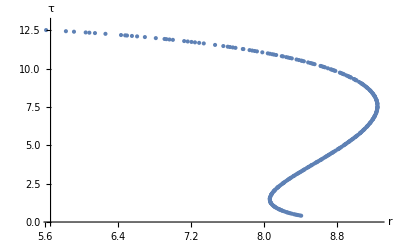

```mathematica
FreezeOutPlot=ListPlot[Transpose[{mydata["Radius"],mydata["Time"]}],AxesLabel->{r,τ}]
```

```mathematica
scale=0.1
```

```mathematica
allvectors=Transpose@{scale*Transpose@{-1*mydata["TimeDerivative"],mydata["RadialDerivative"]},Transpose@{mydata["Radius"],mydata["Time"]}}(*array of single vectors {{vx,vy},{x,y}}*)
```

{{{0.00461432,1.26151},{0.332311,13.012}},{{0.00781469,1.26238},{0.55383,13.011}},{{0.011265,1.26384},{0.775315,13.0093}},{{0.0150261,1.26587},{0.996754,13.007}},{{0.0192199,1.26844},{1.21813,13.004}},{{0.0239051,1.27152},{1.43944,13.0003}},{{0.0292293,1.27504},{1.66066,12.9956}},{{0.035328,1.27895},{1.88178,12.9901}},{{0.0423492,1.28317},{2.10278,12.9834}},{{0.0503588,1.28763},{2.32366,12.9754}},{{0.0596568,1.29218},{2.54441,12.966}},{{0.070167,1.29679},{2.765,12.955}},{{0.0827043,1.30111},{2.98543,12.9421}},{{0.0959527,1.3055},{3.20568,12.927}},{{0.113514,1.30862},{3.42574,12.9094}},{{0.127646,1.31299},{3.6456,12.8891}},{{0.15645,1.31227},{3.86524,12.8657}},{{0.161953,1.31936},{4.08466,12.8387}},{{0.208353,1.31205},{4.30384,12.8078}},{{0.208443,1.31258},{4.31836,12.8055}},{{0.232288,1.31167},{4.52277,12.7725}},{{0.24107,1.31039},{4.57071,12.7638}},{{0.248786,1.3133},{4.74144,12.7324}},{{0.275094,1.31232},{4.95984,12.6869}},{{0.35142,1.28747},{5.17795,12.6356}},{{0.328734,1.3012},{5.295,12.6048}},{{0.372235,1.28558},{5.39577,12.5778}},{{0.378691,1.2834},{5.41657,12.5717}},{{0.378698,1.28601},{5.50995,12.5441}},{{0.397386,1.28093},{5.61328,12.513}},{{0.462713,1.25576},{5.83047,12.4404}},{{0.458491,1.26005},{5.91887,12.4079}},{{0.499772,1.24254},{6.04734,12.3595}},{{0.510735,1.23781},{6.08743,12.3431}},{{0.509341,1.23968},{6.14895,12.3177}},{{0.555895,1.21733},{6.26386,12.2693}},{{0.546682,1.22513},{6.43435,12.1907}},{{0.596465,1.19878},{6.48005,12.1691}},{{0.606233,1.19368},{6.49987,12.1591}},{{0.606664,1.19379},{6.55381,12.1317}},{{0.618297,1.18794},{6.61052,12.1025}},{{0.636159,1.17814},{6.69587,12.0577}},{{0.652717,1.16951},{6.81563,11.9899}},{{0.704573,1.13894},{6.91133,11.9341}},{{0.709144,1.13614},{6.93144,11.9216}},{{0.712894,1.13367},{6.96499,11.9006}},{{0.718296,1.13024},{7.00256,11.8768}},{{0.757532,1.10519},{7.12641,11.7967}},{{0.767988,1.09819},{7.16505,11.7699}},{{0.77283,1.0945},{7.20652,11.7408}},{{0.779434,1.08972},{7.24455,11.7138}},{{0.785064,1.08538},{7.2905,11.6807}},{{0.79845,1.07583},{7.34111,11.6437}},{{0.832775,1.05059},{7.46499,11.5464}},{{0.874508,1.01981},{7.55542,11.4727}},{{0.888053,1.00879},{7.60416,11.4302}},{{0.891205,1.00567},{7.6282,11.409}},{{0.897713,0.99993},{7.65908,11.3815}},{{0.899696,0.997345},{7.68857,11.3549}},{{0.939755,0.96565},{7.76933,11.2806}},{{0.943204,0.962934},{7.77494,11.2751}},{{0.954619,0.950965},{7.84311,11.2076}},{{0.960542,0.94507},{7.87164,11.1787}},{{0.965861,0.939591},{7.89868,11.1511}},{{0.969664,0.935315},{7.92379,11.1252}},{{0.993825,0.913713},{7.98283,11.0631}},{{1.01894,0.890574},{8.0428,10.9955}},{{1.02279,0.885894},{8.06499,10.97}},{{1.02817,0.879668},{8.09167,10.939}},{{1.03274,0.874559},{8.11125,10.916}},{{1.0353,0.870664},{8.13462,10.8883}},{{1.0708,0.83775},{8.19592,10.814}},{{1.0784,0.830444},{8.20986,10.796}},{{1.08427,0.82214},{8.24492,10.7502}},{{1.08931,0.815942},{8.26579,10.7225}},{{1.09395,0.810029},{8.28596,10.6954}},{{1.09734,0.805125},{8.30591,10.6683}},{{1.11761,0.782641},{8.35781,10.5964}},{{1.10696,0.788389},{8.38288,10.5608}},{{1.1389,0.758995},{8.40859,10.5238}},{{1.15075,0.747658},{8.42038,10.5058}},{{1.1475,0.747748},{8.43802,10.4787}},{{1.16469,0.726588},{8.48499,10.4048}},{{1.16915,0.71905},{8.50926,10.3657}},{{1.17326,0.713033},{8.52539,10.3393}},{{1.17725,0.707191},{8.54058,10.3142}},{{1.18006,0.702351},{8.55559,10.2891}},{{1.21866,0.657608},{8.62083,10.1764}},{{1.22155,0.653562},{8.62855,10.162}},{{1.22564,0.646655},{8.64508,10.1309}},{{1.22883,0.641547},{8.65632,10.1095}},{{1.23218,0.635881},{8.66928,10.0845}},{{1.24106,0.621149},{8.701,10.0221}},{{1.24955,0.606484},{8.73215,9.95896}},{{1.25324,0.600156},{8.74492,9.93246}},{{1.2569,0.593654},{8.75822,9.90449}},{{1.26066,0.587198},{8.77064,9.87803}},{{1.26337,0.581677},{8.78288,9.85156}},{{1.29636,0.537913},{8.83263,9.74017}},{{1.30208,0.529029},{8.84444,9.71137}},{{1.30598,0.520962},{8.85868,9.676}},{{1.30885,0.515456},{8.86753,9.65369}},{{1.31194,0.509205},{8.87785,9.62729}},{{1.31995,0.493158},{8.90299,9.56128}},{{1.32519,0.482337},{8.91949,9.51654}},{{1.32899,0.47443},{8.9312,9.48405}},{{1.33133,0.469497},{8.93839,9.4638}},{{1.33402,0.463804},{8.94656,9.44046}},{{1.33669,0.458101},{8.95461,9.41712}},{{1.34714,0.435241},{8.98569,9.32377}},{{1.34958,0.42986},{8.99266,9.30203}},{{1.35256,0.423104},{9.00137,9.27444}},{{1.35492,0.417818},{9.00795,9.25325}},{{1.35742,0.411747},{9.0158,9.22758}},{{1.37736,0.377872},{9.044,9.13134}},{{1.39027,0.354336},{9.06253,9.06069}},{{1.39262,0.347727},{9.06967,9.03242}},{{1.39564,0.339857},{9.07751,9.00062}},{{1.3976,0.334565},{9.08275,8.97891}},{{1.39995,0.328231},{9.08885,8.95316}},{{1.40561,0.312486},{9.10355,8.8888}},{{1.41055,0.298418},{9.11598,8.83149}},{{1.41439,0.287122},{9.12554,8.78535}},{{1.41614,0.281889},{9.12984,8.76398}},{{1.41818,0.275707},{9.13481,8.73873}},{{1.42315,0.260266},{9.14672,8.67559}},{{1.42792,0.244908},{9.15786,8.61271}},{{1.43039,0.236676},{9.16355,8.57895}},{{1.43233,0.230119},{9.16794,8.55204}},{{1.43422,0.223621},{9.17216,8.52534}},{{1.43907,0.20633},{9.18282,8.45414}},{{1.44259,0.193225},{9.19032,8.40001}},{{1.44389,0.18822},{9.19306,8.3793}},{{1.44531,0.182693},{9.196,8.3564}},{{1.44873,0.168913},{9.20295,8.29914}},{{1.45206,0.154864},{9.20949,8.24055}},{{1.45345,0.14875},{9.21217,8.21496}},{{1.45487,0.142378},{9.21484,8.18824}},{{1.45613,0.136538},{9.2172,8.16368}},{{1.45736,0.13071},{9.21945,8.13913}},{{1.46194,0.107537},{9.22746,8.04092}},{{1.46346,0.0992204},{9.22997,8.00542}},{{1.4649,0.0909707},{9.23227,7.97004}},{{1.46572,0.0860703},{9.23354,7.94895}},{{1.46664,0.0803806},{9.23494,7.92439}},{{1.46878,0.0662392},{9.238,7.86298}},{{1.47085,0.0509369},{9.24068,7.79591}},{{1.47184,0.042819},{9.24182,7.76}},{{1.4725,0.0369624},{9.24253,7.73396}},{{1.47308,0.0315248},{9.24309,7.70967}},{{1.47362,0.0261122},{9.24357,7.68537}},{{1.47536,0.00473053},{9.24458,7.58821}},{{1.47616,-0.00912508},{9.24448,7.52415}},{{1.47644,-0.0157395},{9.24422,7.49319}},{{1.47662,-0.0212806},{9.2439,7.46707}},{{1.47672,-0.0255844},{9.24357,7.44666}},{{1.4768,-0.0298642},{9.24319,7.42625}},{{1.47679,-0.0467354},{9.24107,7.3446}},{{1.4767,-0.0515407},{9.24028,7.32098}},{{1.47655,-0.0563527},{9.23941,7.29714}},{{1.47637,-0.0611707},{9.23845,7.27308}},{{1.47572,-0.0727523},{9.23579,7.21442}},{{1.47481,-0.0840997},{9.23267,7.15575}},{{1.47427,-0.0895164},{9.231,7.12727}},{{1.47377,-0.0939759},{9.22952,7.10357}},{{1.47322,-0.0983932},{9.22797,7.07988}},{{1.47059,-0.115622},{9.22108,6.9851}},{{1.46947,-0.121624},{9.21834,6.95112}},{{1.4682,-0.127726},{9.21535,6.91595}},{{1.46742,-0.131243},{9.21354,6.89542}},{{1.4665,-0.135124},{9.21146,6.87251}},{{1.46402,-0.144618},{9.20599,6.81523}},{{1.46116,-0.154188},{9.19991,6.75568}},{{1.45974,-0.158489},{9.19697,6.72822}},{{1.45821,-0.162855},{9.19384,6.69985}},{{1.4569,-0.166385},{9.19121,6.67655}},{{1.45555,-0.169864},{9.18852,6.65326}},{{1.44969,-0.183258},{9.17719,6.56008}},{{1.44636,-0.189907},{9.17093,6.51148}},{{1.44339,-0.195328},{9.16546,6.47043}},{{1.44191,-0.197893},{9.16275,6.45056}},{{1.44015,-0.200813},{9.15957,6.42758}},{{1.43558,-0.207872},{9.1514,6.37011}},{{1.43006,-0.215523},{9.14172,6.30458}},{{1.4266,-0.21987},{9.13576,6.26547}},{{1.4243,-0.2226},{9.13183,6.24015}},{{1.42219,-0.225001},{9.12825,6.21736}},{{1.42004,-0.227349},{9.12462,6.19458}},{{1.41108,-0.236212},{9.10969,6.10345}},{{1.40646,-0.240252},{9.10212,6.05867}},{{1.40226,-0.243648},{9.0953,6.01909}},{{1.40012,-0.245284},{9.09185,5.9993}},{{1.39768,-0.247099},{9.08791,5.97692}},{{1.39137,-0.251328},{9.0779,5.92094}},{{1.38483,-0.255562},{9.06743,5.86356}},{{1.38176,-0.257085},{9.06275,5.83834}},{{1.37848,-0.259124},{9.05744,5.80991}},{{1.37557,-0.260147},{9.05323,5.78761}},{{1.37359,-0.262728},{9.049,5.76532}},{{1.37832,-0.294544},{9.0307,5.67614}},{{1.3711,-0.295776},{9.02014,5.62685}},{{1.3667,-0.29777},{9.0126,5.5921}},{{1.36401,-0.298722},{9.00819,5.57189}},{{1.36111,-0.299761},{9.00337,5.54997}},{{1.35816,-0.30072},{8.99853,5.52804}},{{1.34935,-0.303322},{8.98411,5.4634}},{{1.34356,-0.304758},{8.97472,5.42181}},{{1.33964,-0.305624},{8.96839,5.39399}},{{1.33401,-0.306727},{8.95934,5.35449}},{{1.32662,-0.307933},{8.94752,5.30333}},{{1.32038,-0.308755},{8.9376,5.26074}},{{1.31752,-0.309071},{8.93307,5.24143}},{{1.31431,-0.309385},{8.928,5.21982}},{{1.30621,-0.309985},{8.91523,5.16582}},{{1.29736,-0.310362},{8.90134,5.10753}},{{1.29273,-0.310434},{8.89412,5.07737}},{{1.28886,-0.310444},{8.88807,5.05224}},{{1.28552,-0.310397},{8.88289,5.03076}},{{1.27788,-0.310302},{8.8709,4.98125}},{{1.26373,-0.307985},{8.85026,4.89653}},{{1.25932,-0.316619},{8.83592,4.83806}},{{1.26495,-0.337506},{8.82756,4.80583}},{{1.26292,-0.34108},{8.82086,4.78096}},{{1.25876,-0.33925},{8.81521,4.76002}},{{1.25602,-0.340199},{8.80956,4.73909}},{{1.24098,-0.335771},{8.78687,4.65534}},{{1.23113,-0.335111},{8.76975,4.59234}},{{1.2239,-0.333346},{8.75825,4.5501}},{{1.21973,-0.332411},{8.7515,4.52531}},{{1.21486,-0.331212},{8.74368,4.49664}},{{1.20677,-0.329146},{8.73065,4.44885}},{{1.19853,-0.326874},{8.71742,4.40032}},{{1.19371,-0.325489},{8.70968,4.37195}},{{1.18974,-0.324306},{8.70332,4.34864}},{{1.1823,-0.322027},{8.69138,4.30481}},{{1.17797,-0.320626},{8.68445,4.27934}},{{1.17262,-0.318939},{8.6758,4.24757}},{{1.16418,-0.315715},{8.66258,4.19889}},{{1.15393,-0.313641},{8.6448,4.13331}},{{1.14384,-0.307532},{8.63056,4.08066}},{{1.14224,-0.310447},{8.62505,4.06021}},{{1.1443,-0.322201},{8.61924,4.03919}},{{1.14519,-0.341554},{8.6041,3.98778}},{{1.13351,-0.331293},{8.58902,3.93636}},{{1.13022,-0.33037},{8.583,3.91579}},{{1.12586,-0.328063},{8.57597,3.89169}},{{1.12118,-0.326114},{8.56793,3.86407}},{{1.10976,-0.320179},{8.54919,3.79938}},{{1.09734,-0.314011},{8.52832,3.72675}},{{1.09321,-0.311828},{8.52144,3.70271}},{{1.08902,-0.309617},{8.51445,3.67816}},{{1.07794,-0.303627},{8.49593,3.6127}},{{1.07366,-0.30127},{8.48877,3.58723}},{{1.06915,-0.298785},{8.48118,3.56015}},{{1.06165,-0.294505},{8.46862,3.51501}},{{1.04999,-0.288152},{8.4487,3.4428}},{{1.04551,-0.28525},{8.44134,3.41591}},{{1.04077,-0.283032},{8.43287,3.38481}},{{1.03538,-0.278677},{8.42456,3.35415}},{{1.03119,-0.282268},{8.41281,3.31049}},{{1.03099,-0.296452},{8.4013,3.26962}},{{1.027,-0.295656},{8.39282,3.2402}},{{1.02,-0.289769},{8.38144,3.2004}},{{1.01452,-0.28593},{8.37188,3.1666}},{{1.00988,-0.282246},{8.36407,3.1388}},{{1.00148,-0.275865},{8.34968,3.08691}},{{0.991926,-0.268247},{8.33342,3.02734}},{{0.988175,-0.265242},{8.32701,3.00356}},{{0.984224,-0.262034},{8.32027,2.97835}},{{0.973865,-0.253509},{8.30257,2.91111}},{{0.966554,-0.247359},{8.29007,2.86268}},{{0.962148,-0.243606},{8.28252,2.83305}},{{0.958266,-0.240269},{8.27588,2.80666}},{{0.952689,-0.235413},{8.26632,2.76828}},{{0.947197,-0.230569},{8.25691,2.7299}},{{0.937991,-0.222231},{8.24115,2.6643}},{{0.928047,-0.213026},{8.22411,2.59124}},{{0.925209,-0.210289},{8.21928,2.57009}},{{0.922749,-0.207952},{8.21506,2.55146}},{{0.919596,-0.204809},{8.20973,2.52766}},{{0.916605,-0.202164},{8.20446,2.50386}},{{0.911163,-0.203115},{8.19129,2.44436}},{{0.903424,-0.195975},{8.17726,2.38094}},{{0.894889,-0.184457},{8.16386,2.31753}},{{0.891957,-0.180539},{8.15922,2.29481}},{{0.88958,-0.17729},{8.15549,2.27625}},{{0.887382,-0.174248},{8.15206,2.25891}},{{0.884585,-0.17031},{8.14773,2.23662}},{{0.881823,-0.166348},{8.14348,2.21432}},{{0.874681,-0.15573},{8.13267,2.15541}},{{0.867007,-0.143622},{8.1214,2.08984}},{{0.864688,-0.1398},{8.11808,2.06952}},{{0.862314,-0.135799},{8.11472,2.04846}},{{0.86001,-0.131826},{8.1115,2.02777}},{{0.857736,-0.12781},{8.10837,2.00707}},{{0.852177,-0.117562},{8.10095,1.95533}},{{0.846686,-0.106753},{8.09396,1.90244}},{{0.841387,-0.0955398},{8.08762,1.84954}},{{0.8392,-0.0906552},{8.08513,1.8271}},{{0.837404,-0.0865203},{8.08316,1.80841}},{{0.834978,-0.0807364},{8.08059,1.78272}},{{0.832281,-0.0740174},{8.07788,1.75354}},{{0.825396,-0.0552295},{8.0718,1.67572}},{{0.821477,-0.0432501},{8.069,1.62887}},{{0.817731,-0.0306882},{8.06688,1.58202}},{{0.816178,-0.0251036},{8.06619,1.56188}},{{0.814882,-0.0202538},{8.06572,1.54473}},{{0.81321,-0.0137117},{8.06524,1.52207}},{{0.811389,-0.00618673},{8.06493,1.49667}},{{0.806831,0.0149184},{8.06529,1.42893}},{{0.802737,0.0376322},{8.06749,1.36119}},{{0.800546,0.0519093},{8.06973,1.32098}},{{0.798546,0.0668147},{8.07272,1.28077}},{{0.797506,0.0755086},{8.07474,1.25805}},{{0.796727,0.0825618},{8.07653,1.24001}},{{0.795894,0.0907432},{8.07876,1.21948}},{{0.795075,0.0996018},{8.08137,1.1977}},{{0.793223,0.124168},{8.08954,1.13965}},{{0.792069,0.145773},{8.0978,1.09112}},{{0.791417,0.163884},{8.10542,1.05211}},{{0.791092,0.178078},{8.11182,1.02253}},{{0.790958,0.188003},{8.11648,1.00236}},{{0.790895,0.19827},{8.12148,0.981896}},{{0.790907,0.208942},{8.12682,0.961144}},{{0.791076,0.225174},{8.1353,0.930225}},{{0.791552,0.248298},{8.14758,0.889139}},{{0.792405,0.271556},{8.16106,0.848053}},{{0.7928,0.282161},{8.1668,0.831635}},{{0.793312,0.291617},{8.17274,0.815217}},{{0.793848,0.307179},{8.18025,0.79525}},{{0.79593,0.321214},{8.19592,0.756157}},{{0.796183,0.322834},{8.1977,0.751767}},{{0.797398,0.353412},{8.21159,0.719017}},{{0.799676,0.375546},{8.22819,0.682504}},{{0.802273,0.414949},{8.249,0.640377}},{{0.803495,0.431181},{8.25788,0.623534}},{{0.805595,0.46046},{8.27286,0.596488}},{{0.807608,0.488377},{8.28659,0.573119}},{{0.810348,0.527046},{8.3046,0.544411}},{{0.814287,0.583232},{8.32915,0.508427}},{{0.816997,0.622245},{8.34527,0.4866}},{{0.819458,0.657746},{8.35941,0.468516}},{{0.821964,0.693896},{8.37338,0.451549}},{{0.825338,0.742659},{8.39156,0.430692}},{{0.828609,0.790671},{8.40859,0.412313}}}

```mathematica
somevectors=Downsample[allvectors,5]
```

{{{0.00461432}},{{0.0239051}},{{0.0596568}},{{0.127646}},{{0.232288}},{{0.328734}},{{0.462713}},{{0.555895}},{{0.618297}},{{0.712894}},{{0.779434}},{{0.888053}},{{0.943204}},{{0.993825}},{{1.0353}},{{1.09395}},{{1.15075}},{{1.17725}},{{1.22883}},{{1.2569}},{{1.30598}},{{1.32899}},{{1.34958}},{{1.39027}},{{1.40561}},{{1.42315}},{{1.43907}},{{1.45206}},{{1.46194}},{{1.46878}},{{1.47362}},{{1.47672}},{{1.47637}},{{1.47322}},{{1.4665}},{{1.4569}},{{1.44191}},{{1.4243}},{{1.40226}},{{1.38176}},{{1.3711}},{{1.34935}},{{1.32038}},{{1.29273}},{{1.25932}},{{1.24098}},{{1.20677}},{{1.17797}},{{1.14224}},{{1.12586}},{{1.08902}},{{1.04999}},{{1.03099}},{{1.00148}},{{0.966554}},{{0.937991}},{{0.916605}},{{0.88958}},{{0.867007}},{{0.852177}},{{0.834978}},{{0.816178}},{{0.802737}},{{0.795894}},{{0.791092}},{{0.791552}},{{0.79593}},{{0.803495}},{{0.816997}}}

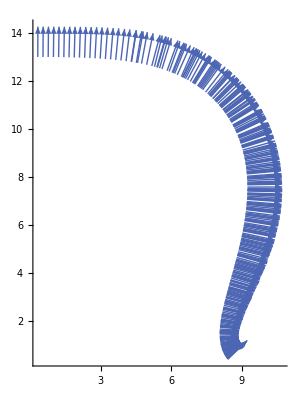

```mathematica
FreezeOutDerivPlot=ResourceFunction["PlotVector"]@allvectors
```

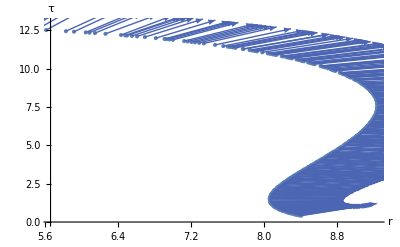

```mathematica
Show[FreezeOutPlot,FreezeOutDerivPlot]
```